```mathematica
Vone:={{1}};
Vmone:={{-1}};
W[k_,n_]:={{Cos[2*Pi*k/n],-Sin[2*Pi*k/n]},{Sin[2*Pi*k/n],Cos[2*Pi*k/n]}};
V[n_]:=If[Mod[n,2]==0,DiagonalMatrix[Hold/@Join[{Vone},Table[W[i,n],{i,1,n/2-1}],{Vmone}]]//ReleaseHold//ArrayFlatten,DiagonalMatrix[Hold/@Join[{Vone},Table[W[i,n],{i,1,n/2}]]]//ReleaseHold//ArrayFlatten];
Cyclic[n_]:=SparseArray[Transpose[{Range[n],PermutationList[Cycles[{Table[n-i+1,{i,1,n}]}],n]}]->1,{n,n}];
Proj[n_]:=Module[{out},
eigsA:=Diagonal[JordanDecomposition[Cyclic[n]][[2]]];
vecsA:=JordanDecomposition[Cyclic[n]][[1]];
ordA:=Ordering[eigsA];
eigsortedA:=eigsA[[ordA]];
vecsortedA:=vecsA[[ordA]];
eigsB:=Diagonal[JordanDecomposition[V[n]][[2]]];
vecsB:=JordanDecomposition[V[n]][[1]];
ordB:=Ordering[eigsB];
eigsortedB:=eigsB[[ordB]];
vecsortedB:=vecsB[[ordB]];
out=vecsortedA.Inverse[vecsortedB];
out
];
wvector[i_,n_]:=Table[-Sin[2*Pi*j*i/n],{j,1,n}];
wwvector[i_,n_]:=Table[Cos[2*Pi*j*i/n],{j,1,n}];
RProj[n_]:=If[Mod[n,2]==0,Transpose[ArrayFlatten[{{Table[1,{i,1,n}]},Flatten[Table[{wvector[i,n],wwvector[i,n]},{i,1,n/2-1}],1],{Table[(-1)^i,{i,1,n}]}},1]],Transpose[ArrayFlatten[{{Table[1,{i,1,n}]},Flatten[Table[{wvector[i,n],wwvector[i,n]},{i,1,n/2}],1]},1]]]
(*--------------*)
RelUBasic[a_]:=If[a<0,0,a];
RelU[list_]:=Table[{RelUBasic[Flatten[list][[i]]]},{i,1,Length[list]}];
AbsBasic[a_]:=If[a<0,-a,a];
AbsF[list_]:=Table[{AbsBasic[Flatten[list][[i]]]},{i,1,Length[list]}];
eMatrix[n_Integer?Positive][i_Integer,j_Integer]/;0<i<=n&&0<j<=n:=Module[{m=ConstantArray[0,{n,n}]},m[[i,j]]=1;m];
UVector[n_,k_]:=Table[{x},{x,UnitVector[n,k]}];
UVector[n_]:=Table[UnitVector[n,k],{k,1,n}];
LRelUBasic[a_]:=If[a<0,0.01*a,a];
LRelU[list_]:=Table[{LRelUBasic[Flatten[list][[i]]]},{i,1,Length[list]}];
PRelUBasic[a_,p_]:=If[a<0,p*a,a];
PRelU[list_,p_]:=Table[{PRelUBasic[Flatten[list][[i]],p]},{i,1,Length[list]}];
FRelUBasic[a_]:=If[a>0,0,a];
FRelU[list_]:=Table[{FRelUBasic[Flatten[list][[i]]]},{i,1,Length[list]}];
SRelUBasic[a_]:=Piecewise[{{-a-3,a<-3},{a+3,-3<a<0},{-2*a+3,0 <=a< 3},{0.5*a-4.5,a>=3}}];
SRelU[list_]:=Table[{SRelUBasic[Flatten[list][[i]]]},{i,1,Length[list]}];
(*--------------*)
MM[n_]:=Table[Flatten[Inverse[RProj[n]].RelU[RProj[n].y]//N],{y,UVector[n]}]//Chop[#]&;
LMM[n_]:=Table[Flatten[Inverse[RProj[n]].LRelU[RProj[n].y]//N],{y,UVector[n]}]//Chop[#]&;
PMM[n_,p_]:=Table[Flatten[Inverse[RProj[n]].PRelU[RProj[n].y,p]//N],{y,UVector[n]}]//Chop[#]&;
FMM[n_]:=Table[Flatten[Inverse[RProj[n]].FRelU[RProj[n].y]//N],{y,UVector[n]}]//Chop[#]&;
AMM[n_]:=Table[Flatten[Inverse[RProj[n]].AbsF[RProj[n].y]//N],{y,UVector[n]}]//Chop[#]&;
SMM[n_]:=Table[Flatten[Inverse[RProj[n]].SRelU[RProj[n].y]//N],{y,UVector[n]}]//Chop[#]&;
(*--------------*)
DivisionOdd[n_]:=Union[{{1}},Table[{i,i+1},{i,Table[i,{i,2,n,2}]}]];
DivisionEven[n_]:=Append[Union[{{1}},Table[{i,i+1},{i,Table[i,{i,2,n-2,2}]}]],{n}];
Division[n_]:=If[Mod[n,2]==0,DivisionEven[n],DivisionOdd[n]];
(*--------------*)
H[a_,b_,n_]:=(MM[n][[Division[n][[a]],Division[n][[b]]]]);
HH[a_,b_,n_]:=MatrixRank[H[a,b,n]];
AdMatrix[n_]:=Table[If[HH[i,j,n]>0,1,0],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
CyGraph[n_]:=AdjacencyGraph[AdMatrix[n],VertexLabels->Table[i->Placed[i-1,Center],{i,1,Length[Division[n]]}],VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->Directive[Thickness[0.005],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink];
(*--------------*)
LH[a_,b_,n_]:=(LMM[n][[Division[n][[a]],Division[n][[b]]]]);
LHH[a_,b_,n_]:=MatrixRank[LH[a,b,n]];
LAdMatrix[n_]:=Table[If[LHH[i,j,n]>0,1,0],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
LCyGraph[n_]:=AdjacencyGraph[LAdMatrix[n],VertexLabels->Placed["Name",Center],VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->Directive[Thickness[0.005],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink];
(*--------------*)
PH[a_,b_,n_,p_]:=(PMM[n,p][[Division[n][[a]],Division[n][[b]]]]);
PHH[a_,b_,n_,p_]:=MatrixRank[PH[a,b,n,p]];
PAdMatrix[n_,p_]:=Table[If[PHH[i,j,n,p]>0,1,0],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
PCyGraph[n_,p_]:=AdjacencyGraph[PAdMatrix[n,p],VertexLabels->Placed["Name",Center],VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->Directive[Thickness[0.005],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink];
(*--------------*)
FH[a_,b_,n_]:=(FMM[n][[Division[n][[a]],Division[n][[b]]]]);
FHH[a_,b_,n_]:=MatrixRank[FH[a,b,n]];
FAdMatrix[n_]:=Table[If[FHH[i,j,n]>0,1,0],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
FCyGraph[n_]:=AdjacencyGraph[FAdMatrix[n],VertexLabels->Placed["Name",Center],VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->Directive[Thickness[0.005],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink];
(*--------------*)
AH[a_,b_,n_]:=(AMM[n][[Division[n][[a]],Division[n][[b]]]]);
AHH[a_,b_,n_]:=MatrixRank[AH[a,b,n]];
AAdMatrix[n_]:=Table[If[AHH[i,j,n]>0,1,0],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
ACyGraph[n_]:=AdjacencyGraph[AAdMatrix[n],VertexLabels->Placed["Name",Center],VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->Directive[Thickness[0.005],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink];
(*--------------*)
SH[a_,b_,n_]:=(SMM[n][[Division[n][[a]],Division[n][[b]]]]);
SHH[a_,b_,n_]:=MatrixRank[SH[a,b,n]];
SAdMatrix[n_]:=Table[If[SHH[i,j,n]>0,1,0],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
SCyGraph[n_]:=AdjacencyGraph[SAdMatrix[n],VertexLabels->Placed["Name",Center],VertexSize->0.5,GraphLayout->"LayeredDigraphEmbedding",EdgeStyle->Directive[Thickness[0.005],Blue],VertexLabelStyle->Directive[20,Blue,Bold],VertexStyle->Pink];
```

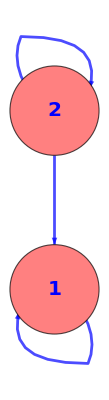
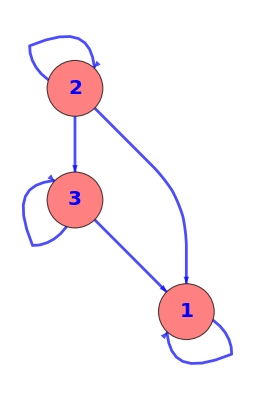
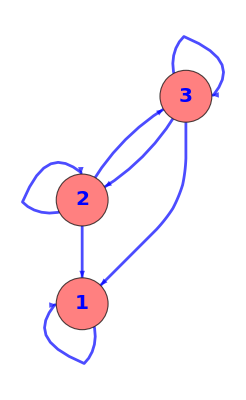
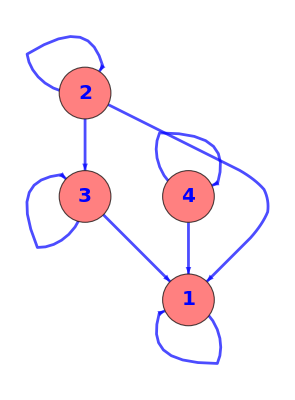
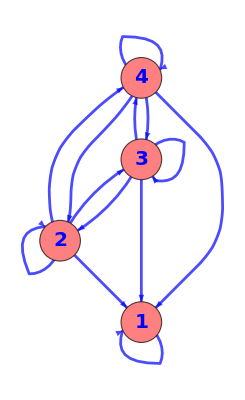
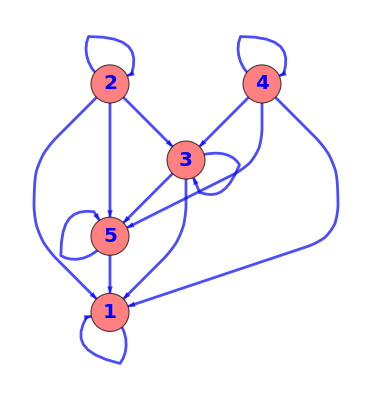

```mathematica
Table[PCyGraph[i,-100],{i,3,8}]
```

```mathematica
Table[PCyGraph[i,-0.5],{i,3,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PCyGraph[i,0.5],{i,3,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PCyGraph[i,0.9],{i,3,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PCyGraph[i,1.1],{i,3,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PCyGraph[i,1.5],{i,3,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PCyGraph[i,100],{i,3,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

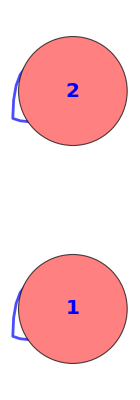
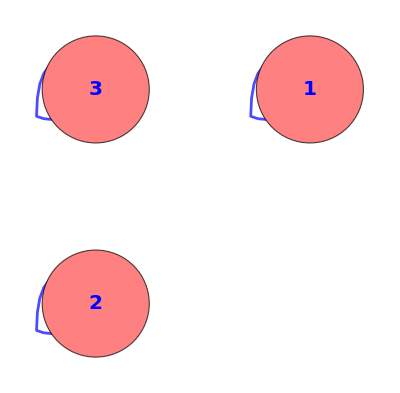
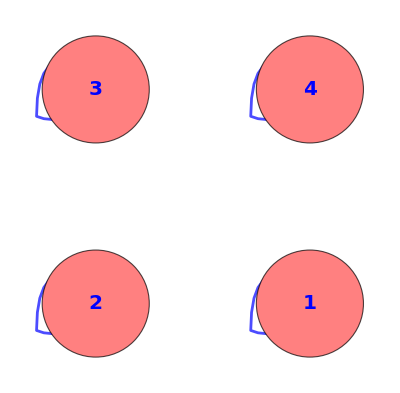
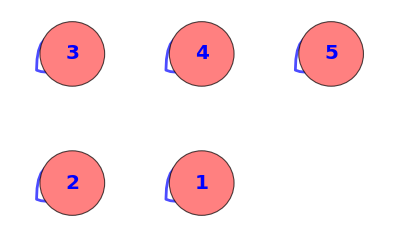
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[PCyGraph[i,1],{i,3,8}]
```

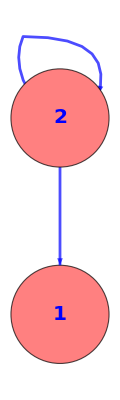
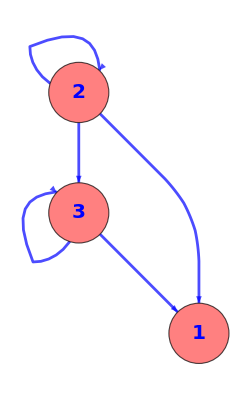
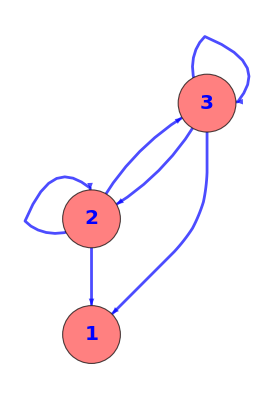
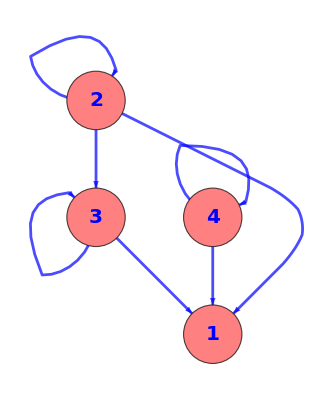
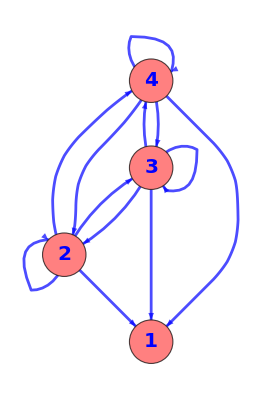
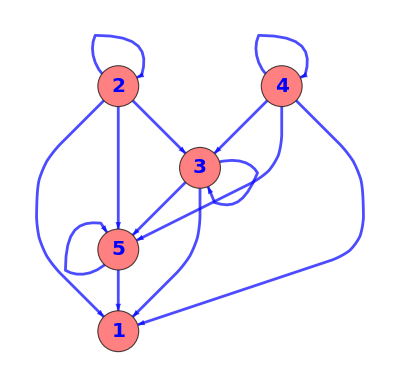

```mathematica
Table[FCyGraph[i],{i,3,8}]
```

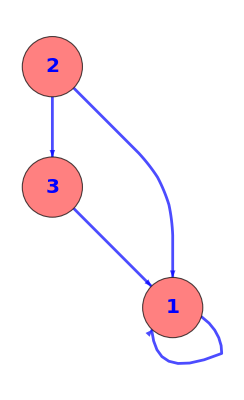
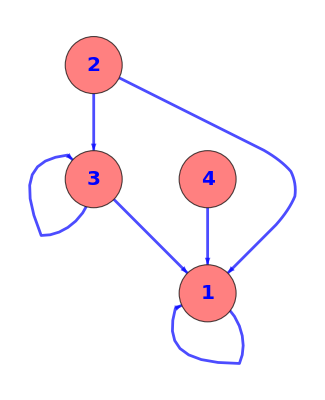
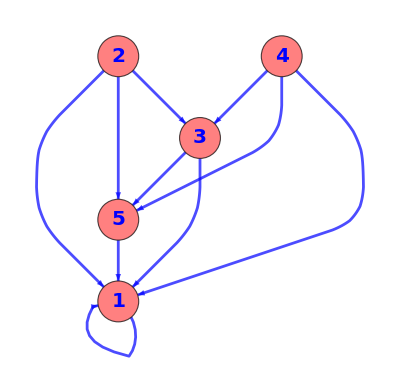
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ACyGraph[i],{i,3,8}]
```

```mathematica
Table[SCyGraph[i],{i,3,8}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(Inverse[RProj[5]].RelU[RProj[5].UVector[5,3]//N]//Chop[#]&)[[1]]
```

{0.323607}

```mathematica
Table[Cos[2*Pi*i/5],{i,0,4}]//N
```

{1.,0.309017,-0.809017,-0.809017,0.309017}

```mathematica
1/5*(2*Cos[2*Pi*1/5]+1)//N
```

0.323607

```mathematica
Inverse[RProj[5]]//MatrixForm
```

(1/5 | 1/5 | 1/5 | 1/5 | 1/5
-2/5 √(5/8+(√5)/8) | -2/5 √(5/8-(√5)/8) | 2/5 √(5/8-(√5)/8) | 2/5 √(5/8+(√5)/8) | 0
(4 (25/8-(5 √5)/8))/(25 √5) | (4 (-25/8-(5 √5)/8))/(25 √5) | (4 (-25/8-(5 √5)/8))/(25 √5) | (4 (25/8-(5 √5)/8))/(25 √5) | 2/5
-2/5 √(5/8-(√5)/8) | 2/5 √(5/8+(√5)/8) | -2/5 √(5/8+(√5)/8) | 2/5 √(5/8-(√5)/8) | 0
(4 (-25/8-(5 √5)/8))/(25 √5) | (4 (25/8-(5 √5)/8))/(25 √5) | (4 (25/8-(5 √5)/8))/(25 √5) | (4 (-25/8-(5 √5)/8))/(25 √5) | 2/5)

```mathematica
RelU[RProj[10].UVector[10,3]//N]//Chop[#]&
```

{{0.809017},{0.309017},{0},{0},{0},{0},{0},{0.309017},{0.809017},{1.}}

```mathematica
Table[Cos[2*Pi*i/10],{i,0,10}]//N
```

{1.,0.809017,0.309017,-0.309017,-0.809017,-1.,-0.809017,-0.309017,0.309017,0.809017,1.}

```mathematica
f[a_,b_]:=({{1,0,0}}.Inverse[RProj[3]].RelU[RProj[3].{{0},{a},{b}}])[[1,1]];
ff[a_,b_]:=({{0,0,0,1}}.Inverse[RProj[4]].RelU[RProj[4].{{0},{a},{b},{0}}])[[1,1]];
g[a_]:=({{1,0,0}}.Inverse[RProj[3]].RelU[RProj[3].{{a},{0},{0}}])[[1,1]];
h[a_,b_]:={({{0,1,0}}.Inverse[RProj[3]].RelU[RProj[3].{{0},{a},{b}}])[[1,1]],({{0,1,0}}.Inverse[RProj[3]].RelU[RProj[3].{{0},{a},{b}}])[[1,1]]};
hh[z_]:=h[Re[z],Im[z]][[1]]+I*h[Re[z],Im[z]][[2]];
fs[a_,b_]:=({{1,0,0}}.Inverse[RProj[3]].AbsF[RProj[3].{{0},{a},{b}}])[[1,1]];
ffs[a_,b_]:=({{0,0,0,1}}.Inverse[RProj[4]].AbsF[RProj[4].{{0},{a},{b},{0}}])[[1,1]];
fl[a_,b_]:=({{1,0,0}}.Inverse[RProj[3]].LRelU[RProj[3].{{0},{a},{b}}])[[1,1]];
ffl[a_,b_]:=({{0,0,0,1}}.Inverse[RProj[4]].LRelU[RProj[4].{{0},{a},{b},{0}}])[[1,1]];
hl[a_,b_]:={({{0,1,0}}.Inverse[RProj[3]].LRelU[RProj[3].{{0},{a},{b}}])[[1,1]],({{0,1,0}}.Inverse[RProj[3]].LRelU[RProj[3].{{0},{a},{b}}])[[1,1]]};
hhl[z_]:=h[Re[z],Im[z]][[1]]+I*h[Re[z],Im[z]][[2]];
```

-Graphics3D-

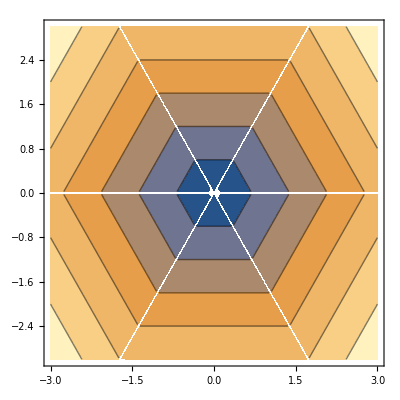

```mathematica
Plot3D[f[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[f[a,b],{a,-3,3},{b,-3,3}]
```

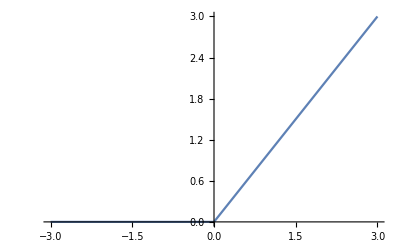

```mathematica
Plot[g[a],{a,-3,3}]
```

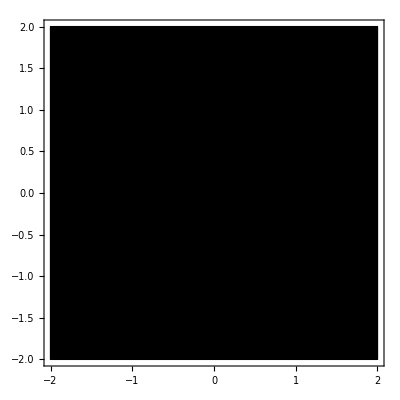

```mathematica
ComplexPlot[hh[z],{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic]
ComplexPlot3D[hh[z],{z,3}]
```

-Graphics3D-

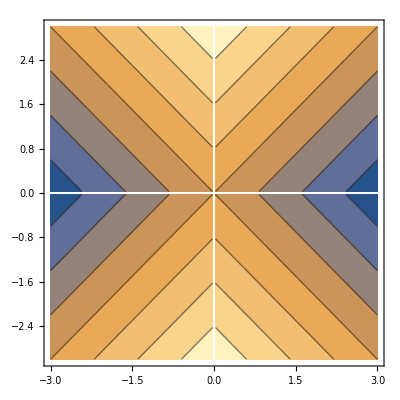

```mathematica
Plot3D[ff[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[ff[a,b],{a,-3,3},{b,-3,3}]
```

-Graphics3D-

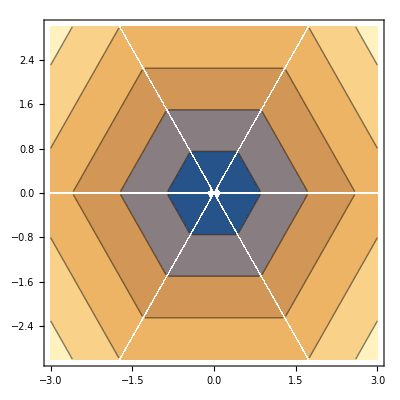

-Graphics3D-

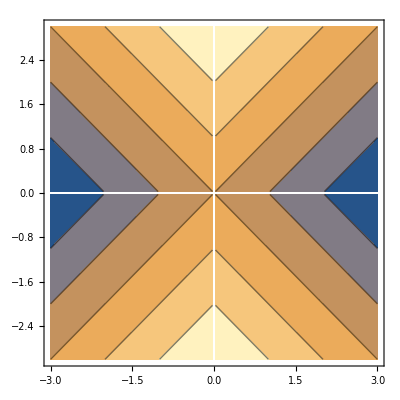

```mathematica
Plot3D[fs[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[fs[a,b],{a,-3,3},{b,-3,3}]
Plot3D[ffs[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[ffs[a,b],{a,-3,3},{b,-3,3}]
```

-Graphics3D-

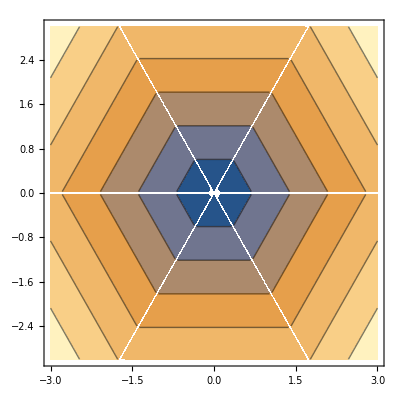

-Graphics3D-

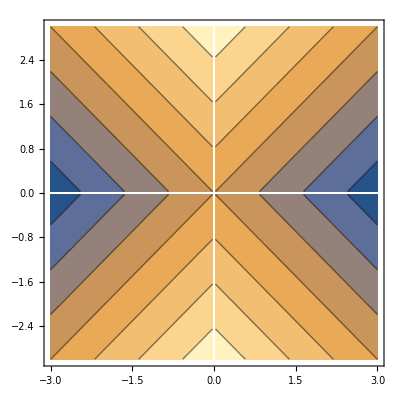

```mathematica
Plot3D[fl[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[fl[a,b],{a,-3,3},{b,-3,3}]
Plot3D[ffl[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[ffl[a,b],{a,-3,3},{b,-3,3}]
```

```mathematica
ComplexPlot[hhl[z],{z,-2-2 I,2+2 I},ColorFunction->"CyclicLogAbsArg",PlotLegends->Automatic]
ComplexPlot3D[hhl[z],{z,3}]
```

-Graphics-

-Graphics3D-

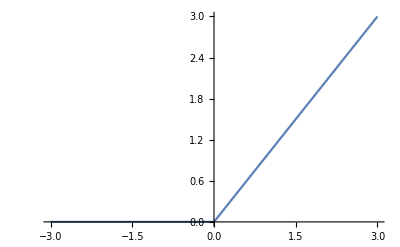

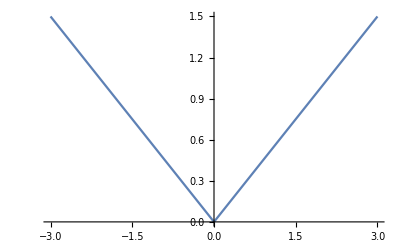

```mathematica
Plot[({{1,0,0,0}}.Inverse[RProj[4]].RelU[RProj[4].{{a},{0},{0},{0}}])[[1,1]],{a,-3,3}]
Plot[({{1,0,0,0}}.Inverse[RProj[4]].RelU[RProj[4].{{0},{0},{0},{a}}])[[1,1]],{a,-3,3}]
```

-Graphics3D-

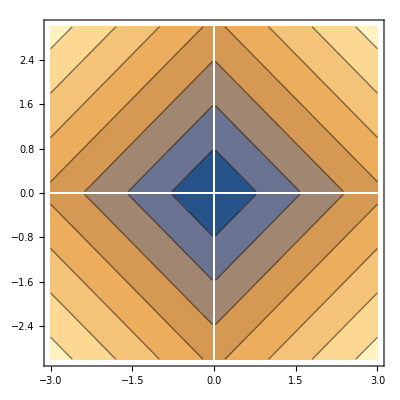

```mathematica
B4=RProj[4]//N;
C4=Inverse[B4]//N;
f4[a_,b_]:=({{1,0,0,0}}.C4.RelU[B4.{{0},{a},{b},{0}}])[[1,1]];
Plot3D[f4[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[f4[a,b],{a,-3,3},{b,-3,3}]
```

-Graphics3D-

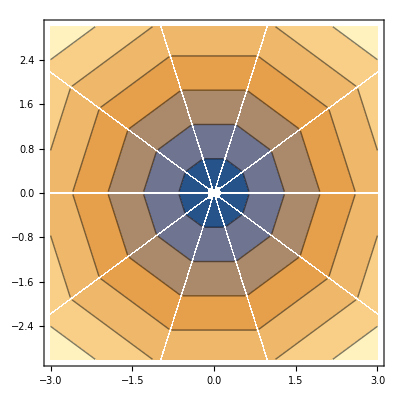

```mathematica
B5=RProj[5]//N;
C5=Inverse[B5]//N;
f5[a_,b_]:=({{1,0,0,0,0}}.C5.RelU[B5.{{0},{a},{b},{0},{0}}])[[1,1]];
Plot3D[f5[a,b],{a,-3,3},{b,-3,3}]
ContourPlot[f5[a,b],{a,-3,3},{b,-3,3}]
```

```mathematica
B6=RProj[6]//N;
C6=Inverse[B6]//N;
f6[a_,b_]:=({{1,0,0,0,0,0}}.C6.RelU[B6.{{0},{a},{b},{0},{0},{0}}])[[1,1]];
Plot3D[f6[a,b],{a,-3,3},{b,-3,3},PlotPoints->100]
ContourPlot[f6[a,b],{a,-3,3},{b,-3,3},PlotPoints->100]
```

-Graphics3D-

-Graphics-

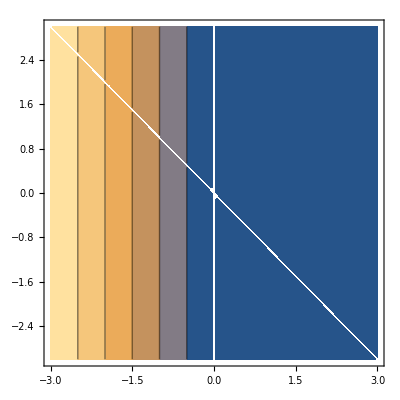

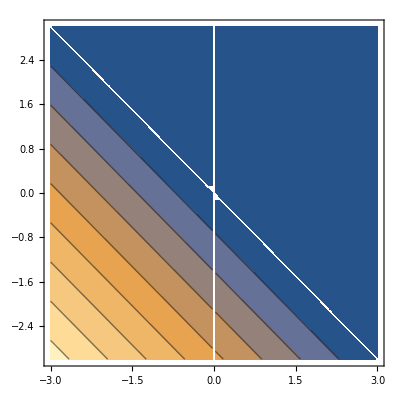

```mathematica
hz8[z_]:=(RelU[RProj[8].{{0},{Re[z]},{Im[z]},{0},{0},{0},{0},{0}}][[2]]+I*RelU[RProj[8].{{0},{Re[z]},{Im[z]},{0},{0},{0},{0},{0}}][[3]])[[1]]
ComplexContourPlot[Re[hz8[z]],{z,-3-3 I,3+3 I}]
ComplexContourPlot[Im[hz8[z]],{z,-3-3 I,3+3 I}]
```

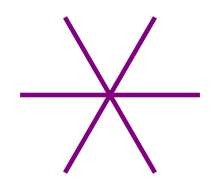
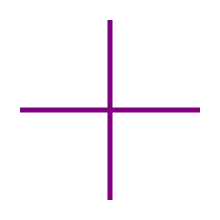
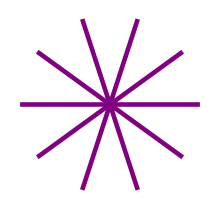
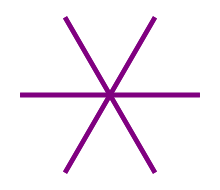
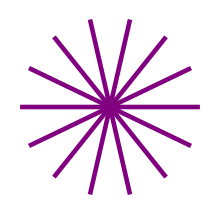
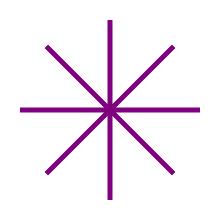

```mathematica
PrintHyperplanes[n_]:=Table[Line[{{(CirclePoints[{1,0},n])[[i]],-(CirclePoints[{1,0},n])[[i]]}}],{i,1,n}];
Table[Graphics[{Purple,Thickness[0.015],PrintHyperplanes[i]},ImageSize->220],{i,3,8}]
```

```mathematica
Subdivide[{-6.6,0},{6.6,0},5]
```

{{-6.6,0},{-3.96,0},{-1.32,0},{1.32,0},{3.96,0},{6.6,0}}

```mathematica
XList=Table[CyGraph[i],{i,1,8}];
Manipulate[XList[[i]],{i,1,8,1}]
```

Part::partd: Part specification XList⟦1⟧ is longer than depth of object.

```mathematica
EmbedCode[CloudDeploy[Manipulate[XList[[i]],{i,1,10,1}]]]
```

Embeddable Code
Use the code below to call the Wolfram Cloud function from HTML:
Code
 | Copy to Clipboard
<iframe src="https://www.wolframcloud.com/obj/d8ae6024-ae14-4898-80ca-7a44f0944ef0?_embed=iframe" width="600" height="800"></iframe>

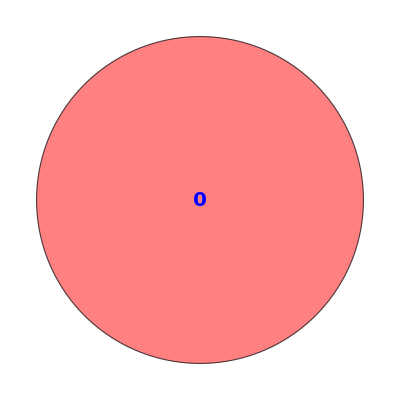
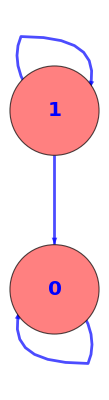
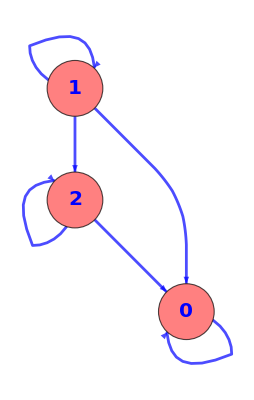
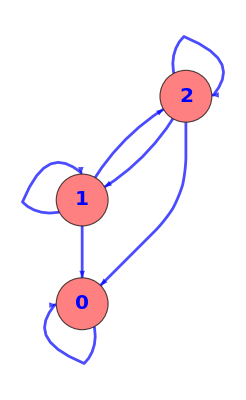
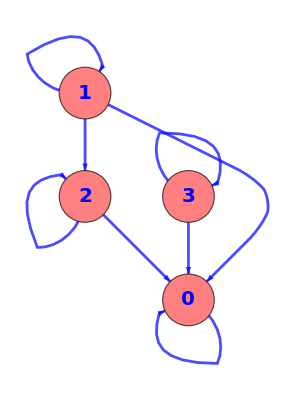
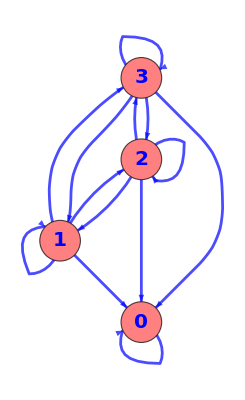
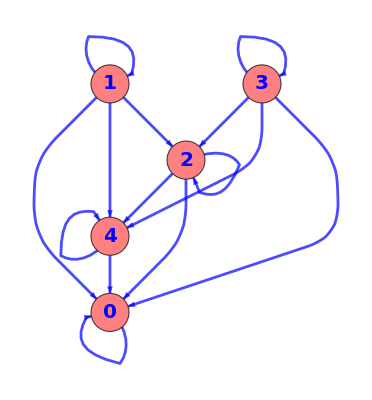
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
XList
```

```mathematica
AdMatrix[9]
```

{{{1}},{{1,0},{1,1}},{{1,0},{1,1}},{{1,0,0},{1,1,1},{1,0,1}},{{1,0,0},{1,1,1},{1,1,1}},{{1,0,0,0},{1,1,1,0},{1,0,1,0},{1,0,0,1}},{{1,0,0,0},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{1,0,0,0,0},{1,1,1,0,1},{1,0,1,0,1},{1,0,1,1,1},{1,0,0,0,1}}}

```mathematica
RelU[RProj[6].UVector[6,2]]//N//MatrixForm
Transpose[RProj[6]].RelU[RProj[6].UVector[6,2]]//N//MatrixForm
RelU[RProj[6].UVector[6,3]]//N//MatrixForm
Transpose[RProj[6]].RelU[RProj[6].UVector[6,3]]//N//MatrixForm
Transpose[RProj[6]]//MatrixForm
```

(0.
0.
0.
0.866025
0.866025
0.)

(1.73205
1.5
0.
0.
-0.866025
0.)

(0.5
0.
0.
0.
0.5
1.)

(2.
0.
1.5
0.
0.5
0.)

(1 | 1 | 1 | 1 | 1 | 1
-(√3)/2 | -(√3)/2 | 0 | (√3)/2 | (√3)/2 | 0
1/2 | -1/2 | -1 | -1/2 | 1/2 | 1
-(√3)/2 | (√3)/2 | 0 | -(√3)/2 | (√3)/2 | 0
-1/2 | -1/2 | 1 | -1/2 | -1/2 | 1
-1 | 1 | -1 | 1 | -1 | 1)

```mathematica
Table[-Sin[2*Pi*i*1/6],{i,1,6}]
Table[Cos[2*Pi*i*1/6],{i,1,6}]
CirclePoints[{1,0},6]
```

{-(√3)/2,-(√3)/2,0,(√3)/2,(√3)/2,0}

{1/2,-1/2,-1,-1/2,1/2,1}

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

```mathematica
OrderAction[n_,k_]:=n/GCD[n,k];
OrderActionP[n_,k_]:=If[Mod[OrderAction[n,k],2]==0,OrderAction[n,k]/2,OrderAction[n,k]];
AdMatOrd[n_]:=Table[If[i==j,1,If[Divisible[OrderActionP[n,i-1],OrderAction[n,j-1]],1,0]],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
AdMatOrdAbs[n_]:=Table[If[Divisible[OrderActionP[n,i-1],OrderAction[n,j-1]],1,0],{i,1,Length[Division[n]]},{j,1,Length[Division[n]]}];
```

```mathematica
Table[AdMatOrd[n],{n,1,20}]
```

{{{1}},{{1,0},{1,1}},{{1,0},{1,1}},{{1,0,0},{1,1,1},{1,0,1}},{{1,0,0},{1,1,1},{1,1,1}},{{1,0,0,0},{1,1,1,0},{1,0,1,0},{1,0,0,1}},{{1,0,0,0},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{1,0,0,0,0},{1,1,1,0,1},{1,0,1,0,1},{1,0,1,1,1},{1,0,0,0,1}},{{1,0,0,0,0},{1,1,1,1,1},{1,1,1,1,1},{1,0,0,1,0},{1,1,1,1,1}},{{1,0,0,0,0,0},{1,1,1,0,1,0},{1,0,1,0,1,0},{1,0,1,1,1,0},{1,0,1,0,1,0},{1,0,0,0,0,1}},{{1,0,0,0,0,0},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1}},{{1,0,0,0,0,0,0},{1,1,1,0,1,0,1},{1,0,1,0,1,0,0},{1,0,0,1,0,0,1},{1,0,0,0,1,0,0},{1,0,1,0,1,1,1},{1,0,0,0,0,0,1}},{{1,0,0,0,0,0,0},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1}},{{1,0,0,0,0,0,0,0},{1,1,1,0,1,0,1,0},{1,0,1,0,1,0,1,0},{1,0,1,1,1,0,1,0},{1,0,1,0,1,0,1,0},{1,0,1,0,1,1,1,0},{1,0,1,0,1,0,1,0},{1,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,0,0,1,0,0,1,0},{1,1,1,1,1,1,1,1},{1,0,0,0,0,1,0,0},{1,0,0,1,0,0,1,0},{1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,1,0,1},{1,0,1,0,1,0,0,0,1},{1,0,1,1,1,0,1,0,1},{1,0,0,0,1,0,0,0,1},{1,0,1,0,1,1,1,0,1},{1,0,0,0,1,0,1,0,1},{1,0,1,0,1,0,1,1,1},{1,0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,1,0,1,0},{1,0,1,0,1,0,1,0,1,0},{1,0,0,1,0,0,1,0,0,0},{1,0,1,0,1,0,1,0,1,0},{1,0,1,0,1,1,1,0,1,0},{1,0,0,0,0,0,1,0,0,0},{1,0,1,0,1,0,1,1,1,0},{1,0,1,0,1,0,1,0,1,0},{1,0,0,0,0,0,0,0,0,1}},{{1,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1}},{{1,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,1,0,1,0,1},{1,0,1,0,1,0,0,0,1,0,0},{1,0,1,1,1,0,1,0,1,0,1},{1,0,0,0,1,0,0,0,1,0,0},{1,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,1,0,1,0,1,0,0},{1,0,1,0,1,0,1,1,1,0,1},{1,0,0,0,1,0,0,0,1,0,0},{1,0,1,0,1,0,1,0,1,1,1},{1,0,0,0,0,0,0,0,0,0,1}}}